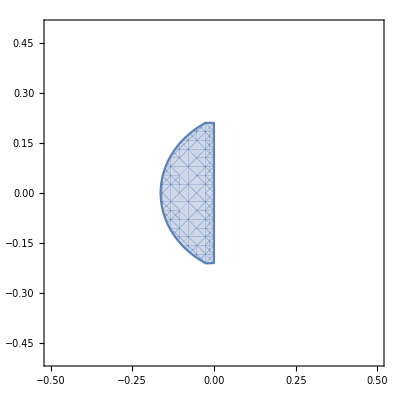

```mathematica
p[z_]:=z^5-z^4;
q[z_]:=(1901z^4-2774z^3+2616z^2-1274z+251)/720;
s=Solve[p[z]-(a+I b)q[z]==0,z];
zeropoints=z/.s;
RegionPlot[Max[Abs[zeropoints]]≤1,{a,-0.5,0.5},{b,-0.5,0.5}]
```

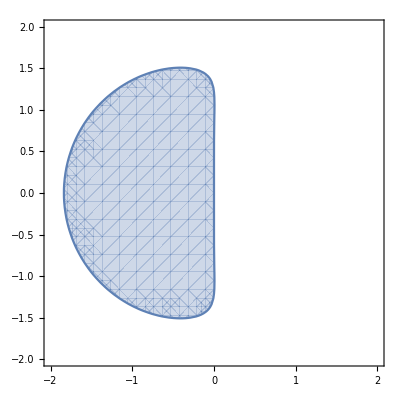

```mathematica
p[z_]:=z^4-z^3;
q[z_]:=(251z^4+646z^3-264z^2+106z-19)/720;
c=Solve[p[z]-(a+I b)q[z]==0,z];
zeropoints=z/.c;
RegionPlot[Max[Abs[zeropoints]]≤1,{a,-2,2},{b,-2,2}]
```